```mathematica
y[n_]:=HermiteH[n,y/a](-1)^n/a^n ⅇ^(-y^2/a^2)
```

```mathematica
y[3]//Expand
```

(12 ⅇ^(-y^2/a^2) y)/a^4-(8 ⅇ^(-y^2/a^2) y^3)/a^6

```mathematica
D[ⅇ^(-y^2/a^2),{y,3}]//Expand
```

(12 ⅇ^(-y^2/a^2) y)/a^4-(8 ⅇ^(-y^2/a^2) y^3)/a^6

```mathematica
D[PDF[NormalDistribution[0,1/(√n)],y-x],{y,5}]//FullSimplify
```

(ⅇ^(-1/2 n (x-y)^2) n^(7/2) (15+n (-10+n (x-y)^2) (x-y)^2) (x-y))/(√(2 π))

```mathematica
htest[k_]:=(-1)^k(n/2)^(k/2)HermiteH[k,√(n/2)(y-x)]PDF[NormalDistribution[0,1/(√n)],y-x]
```

```mathematica
htest[5]//FullSimplify
```

(ⅇ^(-1/2 n (x-y)^2) n^(7/2) (15+n (-10+n (x-y)^2) (x-y)^2) (x-y))/(√(2 π))

```mathematica
htestmean[k_]:=(-1)^k(n/2)^(k/2)HermiteH[k,√(n/2)(y-x)]PDF[NormalDistribution[0,1/(√n)],y-x]
```

```mathematica
htest[3]
```

-(ⅇ^(-1/2 n (-x+y)^2) n^2 (-6 √2 √n (-x+y)+2 √2 n^(3/2) (-x+y)^3))/(4 √π)

```mathematica
HermiteH[3,√(n/2)(y-x)](-1)^3 (n/2)^(3/2)PDF[NormalDistribution[x,1/(√n)],y]//Factor
```

(ⅇ^(-1/2 n (-x+y)^2) n^(5/2) (x-y) (-3+n x^2-2 n x y+n y^2))/(√(2 π))

```mathematica
htestmean[1]
```

-(ⅇ^(-1/2 n (-x+y)^2) n^(3/2) (-x+y))/(√(2 π))

{-2 n (g1-x),-4 n^2 (g1-x)^2,-8 n^3 (g1-x)^3,-16 n^4 (g1-x)^4}

```mathematica
test2[m_]:=∑_(k=0)^m Binomial[m,k](-1)(2n(g1 -x))^(m-k)(-1)^k(n/2)^(k/2)HermiteH[k,√(n/2)(y-x)]PDF[NormalDistribution[0,1/(√n)],y-x]/.y-> g2
```

```mathematica
test2[m_]:=∑_(k=0)^m Binomial[m,k]Evaluate[D[1-Exp[-2n(g2-y)(g1-x)],{y,m-k}]]Evaluate[D[PDF[NormalDistribution[0,1/(√n)],y-x],{y,k}]]/.y-> g2
```

```mathematica
test2[1]//FullSimplify
```

ⅇ^(-1/2 n (g2-x)^2) n^(3/2) √(2/π) (-g1+x)

```mathematica
2n(g1-x)PDF[NormalDistribution[0,1/(√n)],y-x] //FullSimplify
```

ⅇ^(-1/2 n (x-y)^2) n^(3/2) √(2/π) (g1-x)

```mathematica
Table[Evaluate[D[1-Exp[-2n(g2-y)(g1-x)],{y,k}] ]/. y-> g2,{k,1,4}]
```

{-2 n (g1-x),-4 n^2 (g1-x)^2,-8 n^3 (g1-x)^3,-16 n^4 (g1-x)^4}

```mathematica
test2[m_]:=(∑_(k=0)^m Binomial[m,k]Evaluate[D[1-Exp[-2n(g2-y)(g1-x)],{y,m-k}]]Evaluate[D[PDF[NormalDistribution[0,1/(√n)],y-x],{y,k}]])/.y-> g2
```

```mathematica
test4[m_]:=(∑_(k=0)^m Binomial[m,k](-(2n(g1-x))^(m-k))Evaluate[D[PDF[NormalDistribution[0,1/(√n)],y-x],{y,k}]])/.y-> g2
```

```mathematica
{test2[1],test4[1]}//Simplify
```

{ⅇ^(-1/2 n (g2-x)^2) n^(3/2) √(2/π) (-g1+x),(ⅇ^(-1/2 n (g2-x)^2) n^(3/2) (-2 g1+g2+x))/(√(2 π))}

```mathematica
Table[Binomial[m,k]Evaluate[D[1-Exp[-2n(g2-y)(g1-x)],{y,m-k}]]Evaluate[D[PDF[NormalDistribution[0,1/(√n)],y-x],{y,k}]]/. m->1/.y-> g2,{k,0,2}]
```

D::dvar: Multiple derivative specifier {y, -1} does not have the form {variable, n}, where n is a non-negative machine integer.

{-ⅇ^(-1/2 n (g2-x)^2) n^(3/2) √(2/π) (g1-x),(ⅇ^(-1/2 n (g2-x)^2) n^(3/2) (g2-x))/(√(2 π)),0}

```mathematica
Table[Binomial[m,k](-(2n(g1-x))^(m-k))Evaluate[D[PDF[NormalDistribution[0,1/(√n)],y-x],{y,k}]]/.m-> 1/.y-> g2 ,{k,0,2}]
```

{-ⅇ^(-1/2 n (g2-x)^2) n^(3/2) √(2/π) (g1-x),(ⅇ^(-1/2 n (g2-x)^2) n^(3/2) (g2-x))/(√(2 π)),0}

```mathematica
Table[Evaluate[D[1-Exp[-2n(g2-y)(g1-x)],{y,m-k}]] /. m-> 1  /. y -> g2,{k,0,1}]
```

{-2 n (g1-x),-1}

```mathematica
Table[(-(2n(g1-x))^(m-k)) /. m-> 1  /. y -> g2,{k,0,1}]
```

{-2 n (g1-x),-1}

```mathematica
P[x_]:=BernoulliB[1,x-Abs[x]]
```

```mathematica
∫_k^(k+h) P[x/h]ⅆx
```

$Aborted

```mathematica
P[x/h]
```

-1/2+x/h-Abs[x/h]

```mathematica
∫_k^(k+h) (-1/2+x/h-k)ⅆx
```

k-h k

```mathematica
BernoulliB
```

```mathematica
∫_k^(k+h) (-1/2+x/h-k)ⅆx
```

```mathematica
Manipulate[Plot[Evaluate[1/n^l D[(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,l}]] ,{y,-3,g2},PlotRange->Full],{l,0,30,1},{x,-3,g1},{g1,0.5,1},{g2,0.5,1},{n,1,30,1}]
```

```mathematica
a = Table[NIntegrate[Evaluate[Evaluate[1/n^j BernoulliB[j]/(j!)D[(1-Exp[-2n(1-y)(1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,j-1}]]/. y->1/. n-> 10 ],{x,-3,1}] ,{j,2,50,2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.586}. NIntegrate obtained -4.84099×10^-22 and 7.1579×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.476625}. NIntegrate obtained -2.82046×10^-23 and 3.99811×10^-28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.476625}. NIntegrate obtained -1.78604×10^-24 and 2.31357×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{-0.00210261,-3.50435×10^-6,-2.50311×10^-8,-3.12888×10^-10,-5.53086×10^-12,-1.25994×10^-13,-3.50997×10^-15,-1.15576×10^-16,-4.3913×10^-18,-1.89095×10^-19,-9.1007×10^-21,-4.84099×10^-22,-2.82046×10^-23,-1.78604×10^-24,-1.22069×10^-25,-9.21596×10^-27,-6.48689×10^-28,-9.1668×10^-29,4.28534×10^-29,-4.49788×10^-29,4.89167×10^-29,-4.47999×10^-29,2.35509×10^-28,2.85585×10^-29,-5.33275×10^-29}

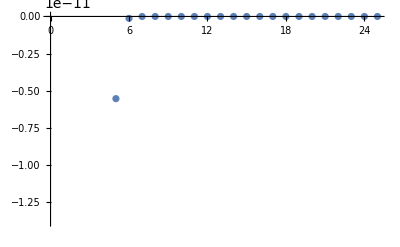

```mathematica
ListPlot[a]
```

```mathematica
Manipulate[Plot[Evaluate[1/n^j BernoulliB[j]/(j!)D[(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x],{y,j-1}]]/.y-> g2,{x,-3,g1},PlotRange->Full],{j,2,10,2},{g1,0.5,1},{g2,0.5,1},{n,1,30,1}]
```